```mathematica
(* a := 2.0 *)
(* d := 1.0 *)
(* En := 10.0 *)
(* k := Sqrt[En] *)
(* P := 3.0 (* Boundary parameter *) *)
```

```mathematica
psi1[x_] := Al * Exp[- I * k * x] + Ar * Exp[I * k * x]
psi2[x_] := Bl * Exp[- I * k * x] + Br * Exp[I * k * x]
```

```mathematica
Solve[psi1[0] == 0, Ar]
```

Solve::ivar: Bl\ ⅇ^-2\ ⅈ\ a\ k\ (ⅇ^2\ ⅈ\ a\ k\ k + ⅇ^2\ ⅈ\ d\ k\ k + ⅈ\ ⅇ^2\ ⅈ\ a\ k\ P - ⅈ\ ⅇ^2\ ⅈ\ d\ k\ P)/(-1 + ⅇ^2\ ⅈ\ d\ k)\ (k + ⅈ\ P) is not a valid variable.

Solve[True,(Bl ⅇ^(-2 ⅈ a k) (ⅇ^(2 ⅈ a k) k+ⅇ^(2 ⅈ d k) k+ⅈ ⅇ^(2 ⅈ a k) P-ⅈ ⅇ^(2 ⅈ d k) P))/((-1+ⅇ^(2 ⅈ d k)) (k+ⅈ P))]

```mathematica
Ar:=-Al
```

```mathematica
Solve[psi2'[a] == P * psi2[a], Br]
```

{{Br→(Bl ⅇ^(-2 ⅈ a k) (k-ⅈ P))/(k+ⅈ P)}}

```mathematica
Br :=(Bl ⅇ^(-2 ⅈ a k) (k-ⅈ P))/(k+ⅈ P)
```

```mathematica
Solve[psi1[d] == psi2[d], Al]
```

{{Al→-(Bl ⅇ^(-2 ⅈ a k) (ⅇ^(2 ⅈ a k) k+ⅇ^(2 ⅈ d k) k+ⅈ ⅇ^(2 ⅈ a k) P-ⅈ ⅇ^(2 ⅈ d k) P))/((-1+ⅇ^(2 ⅈ d k)) (k+ⅈ P))}}

```mathematica
Al:=-(Bl ⅇ^(-2 ⅈ a k) (ⅇ^(2 ⅈ a k) k+ⅇ^(2 ⅈ d k) k+ⅈ ⅇ^(2 ⅈ a k) P-ⅈ ⅇ^(2 ⅈ d k) P))/((-1+ⅇ^(2 ⅈ d k)) (k+ⅈ P))
```

```mathematica
psi1[x]
```

-(Bl ⅇ^(-2 ⅈ a k-ⅈ k x) (ⅇ^(2 ⅈ a k) k+ⅇ^(2 ⅈ d k) k+ⅈ ⅇ^(2 ⅈ a k) P-ⅈ ⅇ^(2 ⅈ d k) P))/((-1+ⅇ^(2 ⅈ d k)) (k+ⅈ P))+(Bl ⅇ^(-2 ⅈ a k+ⅈ k x) (ⅇ^(2 ⅈ a k) k+ⅇ^(2 ⅈ d k) k+ⅈ ⅇ^(2 ⅈ a k) P-ⅈ ⅇ^(2 ⅈ d k) P))/((-1+ⅇ^(2 ⅈ d k)) (k+ⅈ P))

```mathematica
psi2[x]
```

Bl ⅇ^(-ⅈ k x)+(Bl ⅇ^(-2 ⅈ a k+ⅈ k x) (k-ⅈ P))/(k+ⅈ P)

```mathematica
psi2'[d]
```

-ⅈ Bl ⅇ^((0.-1. ⅈ) √En) √En+(ⅈ Bl ⅇ^((0.-3. ⅈ) √En) ((0.-3. ⅈ)+√En) √En)/((0.+3. ⅈ)+√En)

```mathematica
psi1'[d]
```

```mathematica
Solve[psi2'[d] - psi'[d] == psi1[d], En]
```

```mathematica
NSolve[x * Cot[x]==-1,x]
```

Roots::neq: 1 + x\ Cot[x] is expected to be a polynomial in the variable x.

```mathematica
f[x_, k_] := Exp[-I * k * x] - Exp[I * k * x]
```

```mathematica
Integrate[f[x, 2.2889] * f[x, 5.0869],{x,0.0,1.0}]
```

-0.0000526071+0. ⅈ

```mathematica
Integrate[Sin[k * x]^2,x]
```

x/2-Sin[2 k x]/(4 k)

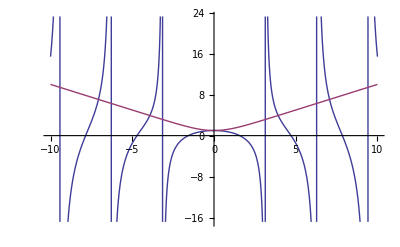

```mathematica
Plot[{x * Cot[x], x * Coth[x]},{x,-10.0,10.0}]
```

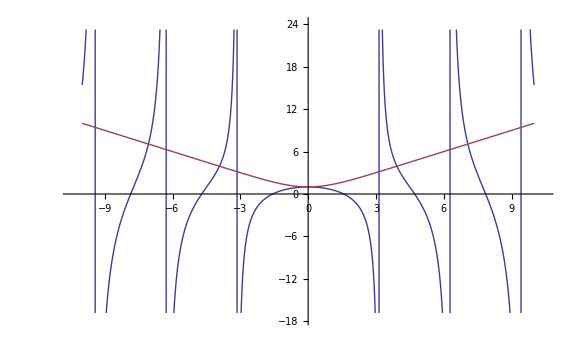

```mathematica
Show[%101,ImageSize->Large]
```

```mathematica
N[Pi / 2 + Pi * 5]
```

17.2788